## Matrix reduction to obtain the transmission coefficient

The system of equations can be rewritten in matrix form,

```mathematica
M=({{1, 1, -1, -1, 0}, {1, -1, α, -α, 0}, {0, 0, ⅇ^(q b), ⅇ^(-q b), -ⅇ^(ⅈ k b)}, {0, 0, -α ⅇ^(q b), α ⅇ^(-q b), -ⅇ^(ⅈ k b)}});
```

```mathematica
M⟦2,All⟧=M⟦2,All⟧- M⟦1,All⟧;
M//MatrixForm//Simplify
```

(1 | 1 | -1 | -1 | 0
0 | -2 | 1+α | 1-α | 0
0 | 0 | ⅇ^(b q) | ⅇ^(-b q) | -ⅇ^(ⅈ b k)
0 | 0 | -ⅇ^(b q) α | ⅇ^(-b q) α | -ⅇ^(ⅈ b k))

```mathematica
M⟦4,All⟧=M⟦4,All⟧+α M⟦3,All⟧;
M//MatrixForm//Simplify
```

(1 | 1 | -1 | -1 | 0
0 | -2 | 1+α | 1-α | 0
0 | 0 | ⅇ^(b q) | ⅇ^(-b q) | -ⅇ^(ⅈ b k)
0 | 0 | 0 | 2 ⅇ^(-b q) α | -ⅇ^(ⅈ b k) (1+α))

```mathematica
M⟦3,All⟧=M⟦3,All⟧-1/(2α) M⟦4,All⟧;
M//MatrixForm//Simplify
```

(1 | 1 | -1 | -1 | 0
0 | -2 | 1+α | 1-α | 0
0 | 0 | ⅇ^(b q) | 0 | -(ⅇ^(ⅈ b k) (-1+α))/(2 α)
0 | 0 | 0 | 2 ⅇ^(-b q) α | -ⅇ^(ⅈ b k) (1+α))

```mathematica
M⟦2,All⟧=M⟦2,All⟧-(1+α)/ⅇ^(b q) M⟦3,All⟧;
M//MatrixForm//Simplify
```

(1 | 1 | -1 | -1 | 0
0 | -2 | 0 | 1-α | (ⅇ^(ⅈ b k-b q) (-1+α) (1+α))/(2 α)
0 | 0 | ⅇ^(b q) | 0 | -(ⅇ^(ⅈ b k) (-1+α))/(2 α)
0 | 0 | 0 | 2 ⅇ^(-b q) α | -ⅇ^(ⅈ b k) (1+α))

```mathematica
M⟦2,All⟧=M⟦2,All⟧-(1-α)/(2 ⅇ^(-b q)α) M⟦4,All⟧;
M//MatrixForm//Simplify
```

(1 | 1 | -1 | -1 | 0
0 | -2 | 0 | 0 | -(ⅇ^(ⅈ b k-b q) (-1+ⅇ^(2 b q)) (-1+α^2))/(2 α)
0 | 0 | ⅇ^(b q) | 0 | -(ⅇ^(ⅈ b k) (-1+α))/(2 α)
0 | 0 | 0 | 2 ⅇ^(-b q) α | -ⅇ^(ⅈ b k) (1+α))

```mathematica
M⟦1,All⟧=M⟦1,All⟧+1/(2 ⅇ^(-b q)α) M⟦4,All⟧;
M//MatrixForm//Simplify
```

(1 | 1 | -1 | 0 | -(ⅇ^(b (ⅈ k+q)) (1+α))/(2 α)
0 | -2 | 0 | 0 | -(ⅇ^(ⅈ b k-b q) (-1+ⅇ^(2 b q)) (-1+α^2))/(2 α)
0 | 0 | ⅇ^(b q) | 0 | -(ⅇ^(ⅈ b k) (-1+α))/(2 α)
0 | 0 | 0 | 2 ⅇ^(-b q) α | -ⅇ^(ⅈ b k) (1+α))

```mathematica
M⟦1,All⟧=M⟦1,All⟧+1/ⅇ^(b q) M⟦3,All⟧;
M//MatrixForm//Simplify
```

(1 | 1 | 0 | 0 | -(ⅇ^(ⅈ b k-b q) (-1+α+ⅇ^(2 b q) (1+α)))/(2 α)
0 | -2 | 0 | 0 | -(ⅇ^(ⅈ b k-b q) (-1+ⅇ^(2 b q)) (-1+α^2))/(2 α)
0 | 0 | ⅇ^(b q) | 0 | -(ⅇ^(ⅈ b k) (-1+α))/(2 α)
0 | 0 | 0 | 2 ⅇ^(-b q) α | -ⅇ^(ⅈ b k) (1+α))

```mathematica
M⟦1,All⟧=M⟦1,All⟧+1/2 M⟦2,All⟧;
M//MatrixForm//Simplify
```

(1 | 0 | 0 | 0 | (ⅇ^(ⅈ b k-b q) ((-1+α)^2-ⅇ^(2 b q) (1+α)^2))/(4 α)
0 | -2 | 0 | 0 | -(ⅇ^(ⅈ b k-b q) (-1+ⅇ^(2 b q)) (-1+α^2))/(2 α)
0 | 0 | ⅇ^(b q) | 0 | -(ⅇ^(ⅈ b k) (-1+α))/(2 α)
0 | 0 | 0 | 2 ⅇ^(-b q) α | -ⅇ^(ⅈ b k) (1+α))

The first line gives us the equationA=-(ⅇ^(ⅈ b k-b q) ((-1+α)^2-ⅇ^(2 b q) (1+α)^2))/(4 α)Fwhich translates in  T=A/F=-(ⅇ^(ⅈ b k-b q) ((-1+α)^2-ⅇ^(2 b q) (1+α)^2))/(4 α) .

Withα=ⅈ q/kbecomesT=(ⅈ ⅇ^(ⅈbk-bq)k((-1+ⅈq/k)^2-ⅇ^(2bq)(1+ⅈq/k)^2))/(4q).

Here we do a little check for some random parameters,

```mathematica
-(4 α)/(ⅇ^(ⅈ b k-b q) ((-1+α)^2-ⅇ^(2 b q) (1+α)^2))/.α->ⅈ q/k/.{q->1.02,k->1.55,b->0.77}//Simplify//N
```

0.441185-0.577206 ⅈ

The result in the video is

```mathematica
(4ⅈ q k ⅇ^(-ⅈ k b))/((2 ⅈ q k+q^2-k^2)ⅇ^(-q b)+(2 ⅈ q k-q^2+k^2)ⅇ^(q b))/.{q->1.02,k->1.55,b->0.77}//Simplify//N
```

0.441185-0.577206 ⅈ

which is in accordance with our value.

## Transmission probability |T|^2 in the limit of large b

In the self-study pack 3, we find 2 expressions of transmission probability, one derived in the limit of large b and the other one as general expression.

In the limit of large b, we find (16 k^2 q^2)/((k^2+q^2)^2)

while the general expression is (4 k^2 q^2)/((k^2+q^2)^2 Sinh[b q]^2+4 k^2 q^2)

Plotting the 2 functions, we see the agreement at large b,

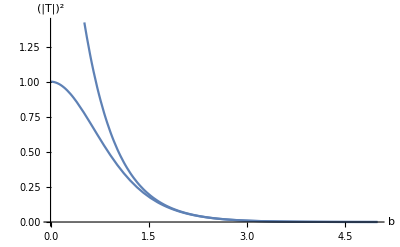

```mathematica
Plot[{(4 k^2 q^2)/((k^2+q^2)^2 Sinh[b q]^2+4 k^2 q^2),(16 k^2 q^2)/((k^2+q^2)^2)ⅇ^(-2 b q)}/.{k->1,q->1},{b,0,5},AxesLabel->{"b", "(|T|)^2"}]
```